Getting the normalization of the spectrum right in 2D, passing from momentum to position space.

Angular integral:

```mathematica
P[k_]:=amp/k^power
```

```mathematica
angularInt=2*Integrate[Exp[I*k*x*Cos[θ]],{θ,0,π}]*k*P[k]*(1/(2π))^2
```

ConditionalExpression[(amp k^(1-power) BesselJ[0,k x])/(2 π), k x∈ℝ]

Rescale:

```mathematica
angularIntRescaled=Assuming[k>0,(angularInt/.k:>k/x)*1/x//PowerExpand//Simplify//Expand]
```

(amp k (x/k)^power BesselJ[0,k])/(2 π x^2)

Integrate:

```mathematica
Integrate[angularIntRescaled,{k,0,∞}]
```

ConditionalExpression[-(2^(-1-power) amp power x^(-2+power) Gamma[-power/2])/(π Gamma[power/2]), 1/2<Re[power]<2]

Agrees w/ result from the NIST site, https://dlmf.nist.gov/10.22#E43, after identities are used

```mathematica
Γidentity=Gamma[1-power/2]/(-power/2 Gamma[-power/2])
%//FullSimplify
```

-(2 Gamma[1-power/2])/(power Gamma[-power/2])

1

Clean up a little

```mathematica
spectrum[amp_,power_]=-(2^(-1-power) amp power x^(-2+power) Gamma[-power/2])/(π Gamma[power/2])*Γidentity
```

(2^-power amp x^(-2+power) Gamma[1-power/2])/(π Gamma[power/2])

Strictly only valid for 2>power>1/2; values outside this range defined by analytic continuation/ regularization.

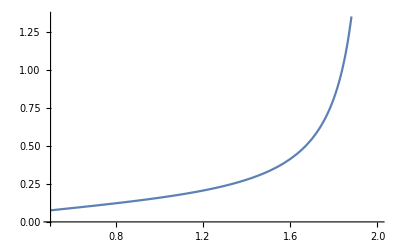

```mathematica
Plot[spectrum[1,power]/.x:>1,{power,1/2,2}]
```